# Fisher estimates for a power law mass spectrum

```mathematica
SetDirectory@NotebookDirectory[];
<<MaTeX`
```

## No selection effects

## Inputs

```mathematica
$Assumptions={θ>0,θmax>0,θmin>0,θmax>θmin, σ>0 & σ<1000,λ>-1}
```

{θ>0,θmax>0,θmin>0,θmax>θmin,σ (σ>0&)<1000,λ>-1}

In this first example we do not consider selection effects, meaning we set the probability of detection for both source and population parameters to one.

```mathematica
pdetθ[M_]:=1
pdetλ[λ_]:=1
ppop[{θ_,θmin_,θmax_},λ_]:= λ/(θmax^λ-θmin^λ) θ^(λ-1)
```

We check here that the population model is correctly normalized.

```mathematica
Integrate[ppop[{θ,θmin,θmax},λ],{θ,θmin,θmax}]
```

1

A bunch of useful quantities that enter the Fisher matrix.

```mathematica
Γ = 1/σ^2;  (* True only in the case in which d = θ + noise. *)
Dmij= Γ ;  (* Only true in the absence of selection effects. *)
Dmi = D[pdetθ[θ],θ];
P = D[Log@ppop[{θ,θmin,θmax},λ],θ];
H = - D[D[Log@ppop[{θ,θmin,θmax},λ],θ],θ];
```

Choose the true parameters here.

```mathematica
λtrue =0.00001;
truepars ={Nobs->1000,λ->λtrue,σ->0.1,θmax->10^7, θmin->10^4}//N;
```

## Fisher matrix and precision estimates [only retaining first term]

In this simplified scenario, we only consider the first (dominant) contribution to the Fisher matrix, without considering selection effects.
Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
SimpPopFisherNoSelectionEffects[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=
Integrate[(1/ppop[{θ,θmin,θmax},λ])D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,θmin,θmax}]
```

```mathematica
ΓλλSimpNoSelectionEffects = SimpPopFisherNoSelectionEffects[λ,{M,10^4,10^7},{λ,λ}];//Timing
```

{16.1982,Null}

```mathematica
ΓλλSimpNoSelectionEffects
```

1/λ^2-(9 1000^λ Log[10]^2)/((-1+1000^λ)^2)

```mathematica
√(1/(Nobs*ΓλλSimpNoSelectionEffects))
Δα =%/.truepars
```

√(1/(Nobs (1/λ^2-(9 1000^λ Log[10]^2)/((-1+1000^λ)^2))))

0.0158814

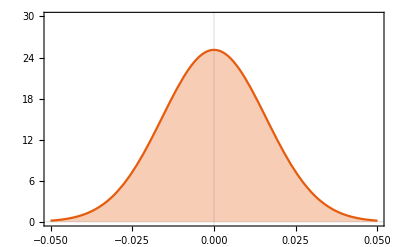

```mathematica
SimplifiedFisher=Plot[
PDF[NormalDistribution[λtrue,Δα],x]//Evaluate,{x,-.05,.05},
Filling->Axis,PlotRange->{All,{0,30}},
FrameLabel->{{MaTeX["\\text{PDF}",FontSize->17],None},{MaTeX["\\alpha_0",FontSize->17],None}},
FrameTicksStyle->Directive[Black,13],
TicksStyle->Directive[Black,AbsoluteThickness[100]],
PlotTheme-> "Scientific", 
Frame->True]
```

## Fisher matrix and precision estimates [including all terms]

Notice that M is integrated out in the interval 10^4 M_0< M < 10^7 M_0.

```mathematica
Γλλ=With[{θmin =10^4 ,θmax = 10^7,Γ = Γ, H = H, D2 = Dmij,D1=Dmi},
model = ppop[{θ,θmin,θmax},λ];
a = Integrate[(pdetθ[θ]/(model pdetλ[λ]))D[model,λ]*D[model,λ],{θ,θmin,θmax}];
b = - 1/pdetλ[λ]^2 D[pdetλ[λ],λ]*D[pdetλ[λ],λ];
c = 1/2 Integrate[D[D[Log@(Γ+H),λ],λ] pdetθ[θ]/pdetλ[λ] model,{θ,θmin,θmax}];
d =-1/2 Integrate[D[D[(Γ+H)^-1,λ],λ]D2 model/pdetλ[λ],{θ,θmin,θmax}];
e =- Integrate[D[D[P(Γ+H)^-1,λ],λ]D1 model/pdetλ[λ],{θ,θmin,θmax}];
f = -Integrate[D[D[P^2(Γ+H)^-1,λ],λ] model/pdetλ[λ],{θ,θmin,θmax}];
a+b+c+d+e+f
];//Timing
```

{59.7318,Null}

```mathematica
√(1/(Nobs*Γλλ));
%/.truepars
Δαfull=Re[%]
```

0.0158814+8.87709×10^-10 ⅈ

0.0158814

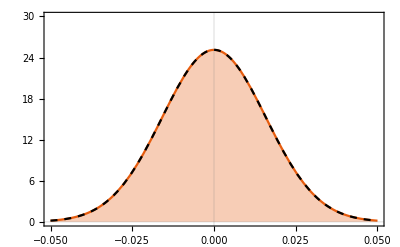

```mathematica
FullFisher = Plot[PDF[NormalDistribution[λtrue,Δαfull],x]//Evaluate,{x,-.05,.05},PlotStyle->{Black,Dashed}];
Show[SimplifiedFisher,FullFisher]
```

```mathematica
(*PopFisherNoSelectionEffects[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=(*TO FIX: issue in integration of higher orders. *)
Integrate[(1/ppop[{θ,θmin,θmax},λ])D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,10^4,10^7}] +1/2 Integrate[D[D[Log@(Γ+H),j],i]ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}]-1/2 Integrate[D[D[(Γ+H)^-1,j],i]Dmij ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}] - Integrate[D[D[P(Γ+H)^-1,j],i]Dmi ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}] -Integrate[D[D[P^2(Γ+H)^-1,j],i]*ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}] *)
```

```mathematica
(*Γλλfct = PopFisherNoSelectionEffects[λ,{M,10^4,10^7},{λ,λ}];//Timing (*Useful to debug*) *)
```

## With selection effects

## Generic case [to do]

```mathematica
(*PopFisher[λ_,{θ_,θmin_,θmax_},{i_,j_}]:=
Integrate[(pdetθ[θ]/(ppop[{θ,θmin,θmax},λ]*pdetλ[λ]))D[ppop[{θ,θmin,θmax},λ],i]*D[ppop[{θ,θmin,θmax},λ],j],{θ,10^4,10^7}]- 1/pdetλ[λ]^2 D[pdetλ[λ],i]*D[pdetλ[λ],j] +1/2 Integrate[D[D[Log@(Γ+H),j],i] pdetθ[θ]/pdetλ[λ] ppop[{θ,θmin,θmax},λ],{θ,10^4,10^7}]-1/2 Integrate[D[D[(Γ+H)^-1,j],i]Dmij ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] - Integrate[D[D[P(Γ+H)^-1,j],i]Dmi ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] -Integrate[D[D[P^2(Γ+H)^-1,j],i] ppop[{θ,θmin,θmax},λ]/pdetλ[λ],{θ,10^4,10^7}] *)
```